```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis\\mNStar"]];
Print["(DescDir) Rawdata Directory: ",descDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\Prajwal\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\Pictures\\nstar"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\system"];
];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis\mNStar

(DescDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\Prajwal\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\Prajwal\Dropbox\nEDM\Pictures\nstar

(SysDir) System Directory: C:\Users\Prajwal\Dropbox\nEDM\system

```mathematica
descdat=ReadList[StringJoin[descDir,"\\","desc.dat"],{Word,Word,Word,Number,Number,Number,Number,Word}];
Print["Runs in the list: ",runNum=descdat[[;;,4]]];
Print["Storage time in the list: ",ts2=descdat[[;;,7]]];
Print["#Runs in the list: ",runn=Dimensions[runNum][[1]]];
bkgcou=Table[{},{k,1,runn}];moncou=Table[0,{k,1,runn}];
moncou=Table[{},{k,1,runn}];moncou=Table[0,{k,1,runn}];
Monitor[
ptdat2=Table[Table[{0,{0,0}},{k,1,Round[(histlast2-histbeg2)/binw2]}],{l,1,runn}];
histbeg2=0*(10^9);histlast2=600*(10^9);binw2=1*(10^9);
For[runi=1,runi≤runn,runi++,
Clear[data,histdata2];
maxCy=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_Meta3.edm"],metaStructure2][[-1]][[2]];
bkgcou[[runi]]={};
moncou[[runi]]={};
icycle=1;
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_UCNdet_",IntegerString[icycle,10,3],"_0001.fast.ascii"],metaStructure];
Print["Read Run #",runNum[[runi]]];
dimdata=Dimensions[data][[1]];
histdata2=HistogramList[data[[1;;dimdata,4]],{histbeg2,histlast2,binw2}];
For[i=1,i<=Dimensions[histdata2[[2]]][[1]],i++,
ptdat2[[runi]][[i]][[1]]=(histdata2[[1]][[i]]+((-histdata2[[1]][[1]]+histdata2[[1]][[2]])/2))/(10^9);
ptdat2[[runi]][[i]][[2]][[1]]=histdata2[[2]][[i]];
ptdat2[[runi]][[i]][[2]][[2]]=Sqrt[ptdat2[[runi]][[i]][[2]][[1]]];
];
];,
ProgressIndicator[runi/runn,ImageSize->{1000,100}]]
ProgressIndicator[1,ImageSize->{1000,100}]
```

Runs in the list: {12693,12695,12697,12704,12707,12770,12771,12772,12773,12774,12775,12778,12779,12780,12781}

Storage time in the list: {180,180,180,380,380,200,220,240,260,280,300,320,340,360,300}

#Runs in the list: 15

Read Run #12693

Read Run #12695

Read Run #12697

Read Run #12704

Read Run #12707

Read Run #12770

Read Run #12771

Read Run #12772

Read Run #12773

Read Run #12774

Read Run #12775

Read Run #12778

Read Run #12779

Read Run #12780

Read Run #12781

```mathematica
Clear[nlm,aa]
stft=10;
endft=55;
pt=Table[0,{k,1,runn}];
ptft=Table[{0,{0,0}},{k,1,runn}];
For[icycle=1,icycle≤runn,icycle++,
Print["Cycle # ",runNum[[icycle]]];
ftdat=Table[Transpose[{ptdat2[[icycle]][[;;,1]],ptdat2[[icycle]][[;;,2]][[;;,1]]}][[k]],{k,Round[30+ts2[[icycle]]+stft],Round[30+ts2[[icycle]]+stft+endft]}];
nlm=NonlinearModelFit[ftdat,{aa+(bb Exp[cc (xx-dd)])},{{aa,1},{bb,30000},{cc,-.4},{dd,33}},xx,Method->NMinimize];
fitparam={aa/.nlm[[1]][[2]],bb/.nlm[[1]][[2]],cc/.nlm[[1]][[2]],dd/.nlm[[1]][[2]]};
fitparamerr=SetPrecision[N[nlm["ParameterErrors"]],10];
pt[[icycle]]=Show[{
EDALogListPlot[ptdat2[[icycle]]+.1, PlotStyle->{Blue},Joined->True,Filling->Axis,PlotRange->{{0,600},{1,100000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, Medium},
PlotLabel->StringJoin["t_s = ",ToString[Round[23+ts2[[icycle]]]]," s, N_EmptyingExp[",ToString[fitparam[[3]]],"(t-t_0)]"]],
EDALogListPlot[Table[{k,Abs[fitparam[[1]]+fitparam[[2]]Exp[fitparam[[3]](k-fitparam[[4]])]]},{k,Round[30+ts2[[icycle]]+stft],Round[30+ts2[[icycle]]+stft+endft]}], PlotStyle->{Red},Joined->True,Filling->Axis,PlotRange->{{0,600},{.1,40000}},Frame->True,FrameLabel->{"Time (s)","# UCN Counts"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic, None}]
}];
ptft[[icycle]]={Round[23+ts2[[icycle]]],{-(1/PlusMinus[fitparam[[3]],fitparamerr[[3]]])[[1]],2(1/PlusMinus[fitparam[[3]],fitparamerr[[3]]])[[2]]}};
];
width=3;
exppt=GraphicsGrid[ArrayReshape[pt,{Ceiling[runn/width],width}]];
```

Cycle # 12693

Cycle # 12695

Cycle # 12697

Cycle # 12704

Cycle # 12707

Cycle # 12770

Cycle # 12771

Cycle # 12772

Cycle # 12773

Cycle # 12774

Cycle # 12775

Cycle # 12778

Cycle # 12779

Cycle # 12780

Cycle # 12781

```mathematica
Export[StringJoin[PicDir,"\\","t_emptying2.png"],exppt]
```

C:\Users\Prajwal\Dropbox\nEDM\Pictures\nstar\t_emptying2.png

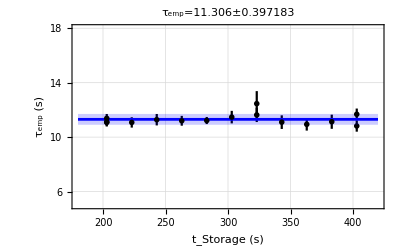

```mathematica
Show[{
EDAListPlot[ptft,PlotRange->{{180,420},{5,18}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"t_Storage (s)","τ_emp (s)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Red,Medium},PlotLabel->StringJoin["τ_emp=",ToString[Mean[ptft[[;;,2]][[;;,1]]]],"±",ToString[StandardDeviation[ptft[[;;,2]][[;;,1]]]]]],
Plot[{Mean[ptft[[;;,2]][[;;,1]]],Mean[ptft[[;;,2]][[;;,1]]]+StandardDeviation[ptft[[;;,2]][[;;,1]]],Mean[ptft[[;;,2]][[;;,1]]]-StandardDeviation[ptft[[;;,2]][[;;,1]]]},{x,180,420},Filling->{2->{3}},FillingStyle->{Opacity[.5],Blue},PlotStyle->{{Blue,Thickness[.005]},None,None}]
}]
```

```mathematica
StringJoin["τ_emp=",ToString[Mean[ptft[[;;,2]][[;;,1]]]],"±",ToString[StandardDeviation[ptft[[;;,2]][[;;,1]]]]]
```

τ_emp=11.306±0.397183